#### I have a list of solutions from `Solve[]` in the form

```mathematica
sol ={
{A-> 3 a, B-> 2 -b,C-> a*b} ,
{A-> 5 a, B-> 2 +b,C-> a/b},
{A-> 0.5 a, B-> 2 b,C-> a-b}
};
```

{3 a>0&&0≤2-b≤1&&a b>0,5 a>0&&0≤2+b≤1&&a/b>0,0.5 a>0&&0≤2 b≤1&&a-b>0}

3 a>0&&0≤2-b≤1&&a b>0
5 a>0&&0≤2+b≤1&&a/b>0
0.5 a>0&&0≤2 b≤1&&a-b>0

#### where `a` and `b` are as yet unspecified parameters.

#### I would like to assess the truth of various conditions on each solution/row (evaluated after specifying `a` and `b`): a condition for the `A`’s, a condition on each `B`’s, etc...

#### For example, for the `A`’s

```mathematica
As=#>0 &/@ sol[[;;,1,2]]
```

{3 a>0,5 a>0,0.5 a>0}

#### for the `B`’s

```mathematica
Bs=0 ≤ #< 1 &/@ sol[[;;,2,2]]
```

{0≤2-b<1,0≤2+b<1,0≤2 b<1}

#### and for the `C`' s.

```mathematica
Cs=#> 0 &/@ sol[[;;,3,2]]
```

{a b>0,a/b>0,a-b>0}

#### Thus, together :

```mathematica
solCond=Transpose[{As,Bs, Cs}];
solCond//TableForm
```

3 a>0 | 0≤2-b<1 | a b>0
5 a>0 | 0≤2+b<1 | a/b>0
0.5 a>0 | 0≤2 b<1 | a-b>0

#### I then want to evaluate at a given set of parameter values

```mathematica
par = {a-> 2, b-> 2};
solCond/.par//TableForm
```

True | True | True
True | False | True
True | False | False

#### and then assess whether all conditions are satisfied by each solution.

```mathematica
And@@@solCond/.par
```

{True,False,False}

#### My ultimate goal is to supply the result to `RegionPlot[]`.

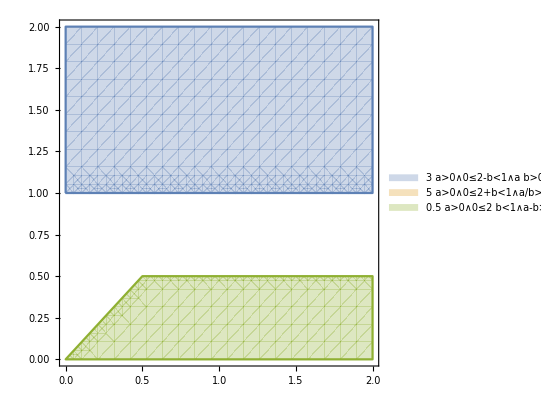

```mathematica
RegionPlot[
Evaluate[And@@@solCond],
{a,0,2},
{b,0,2},
PlotLegends->"Expressions"]
```

#### My list of solutions is relatively large (5 x 28) and I wish to assess different sets of conditions for different plots. I therefore desire a more efficient and general way of specifying and applying the conditions on the `A`’s, `B`’s, `C`’s. There’s got to be a simple way to write a function to apply to each row of `sol` that takes in the conditions as arguments, but I am naive enough about Mathematica that I can’t figure out how to do that and use `Slots[]` or `Parts[]` to apply them appropriately.

```mathematica
par = {a-> 2, b-> 2};
out = A>0&&0≤B≤1&&C>0/.sol
out/.par
```

{3 a>0&&0≤2-b≤1&&a b>0,5 a>0&&0≤2+b≤1&&a/b>0,0.5 a>0&&0≤2 b≤1&&a-b>0}

{True,False,False}